```mathematica
dataV={35,44,51,61,76,90,103,110,124,135,147,159,172,188,200,211,227,238,248};
```

```mathematica
dataVd={0.1,0.4,0.8,1.9,4.8,10.4,17.4,23.1,36.3,50.4,67.6,89.4,117.6,157.4,193.6,228,285,319,343}*10^(-3);
```

```mathematica
dataI={240,274,296,326,366,404,435,451,482,506,529,552,577,606,627,646,673,691,707}*10^(-3);
```

```mathematica
(*PARTE 4.1*)
```

```mathematica
datalnP=Log[dataI*dataV];
```

```mathematica
datalnR=Log[dataV/dataI];
```

```mathematica
datap1=Transpose[{datalnR,datalnP}];
```

```mathematica
fit1=NonlinearModelFit[datap1,A+4*G*x,{A,G},x]
```

FittedModel[…]

```mathematica
fit1[{"BestFit","ParameterTable"}]
```

{-15.0493+3.44862 x, | Estimate | Standard Error | t-Statistic | P-Value
A | -15.0493 | 0.0462538 | -325.363 | 1.06741×10^-33
G | 0.862156 | 0.00208835 | 412.84 | 1.86427×10^-35}

```mathematica
plotfit1=Plot[fit1[x],{x,4.4,5.9},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{4.9,5.9},{2,5.6}},Frame->True,FrameLabel->{Style["Ln( R / Ω )",Bold,16],Style["Ln( P / W )",16,Bold]}];
```

```mathematica
plotdata1=ListPlot[datap1,PlotStyle->{Black,Thickness[0.003]}];
```

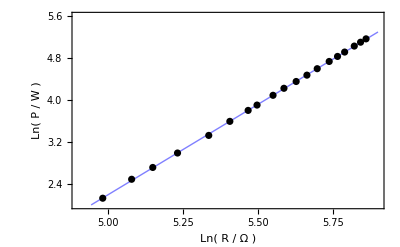

```mathematica
Show[plotfit1,plotdata1]
```

```mathematica
S[A_,G_,R0_,T0_,sigm_]:=Exp[A]*R0^(4*G)/(sigm*T0^4)
```

```mathematica
S[-15.049257050057296,0.862156,25,295,5.67*10^-8] (*valor de S*)
```

0.0000449044

```mathematica
D[S[A,G,R0,T0,sigm],A]
```

(ⅇ^A R0^(4 G))/(sigm T0^4)

```mathematica
dA[A_,G_,R0_,T0_,sigm_]:=(ⅇ^A R0^(4 G))/(sigm T0^4)
```

```mathematica
dAA=dA[-15.049257050057296,0.862156,25,295,5.67*10^-8]
```

0.0000449044

```mathematica
D[S[A,G,R0,T0,sigm],G]
```

(4 ⅇ^A R0^(4 G) Log[R0])/(sigm T0^4)

```mathematica
dG[A_,G_,R0_,T0_,sigm_]:=(4 ⅇ^A R0^(4 G) Log[R0])/(sigm T0^4)
```

```mathematica
dGG=dG[-15.049257050057296,0.862156,25,295,5.67*10^-8]
```

0.000578167

```mathematica
D[S[A, G, R0, T0, sigm], R0]
```

(4 ⅇ^A G R0^(-1+4 G))/(sigm T0^4)

```mathematica
dR0[A_,G_,R0_,T0_,sigm_]:=(4 ⅇ^A G R0^(-1+4 G))/(sigm T0^4)
```

```mathematica
dRR=dR0[-15.049257050057296,0.862156,25,295,5.67*10^-8]
```

6.19434×10^-6

```mathematica
errSd1=Sqrt[(0.10217155108411698*dAA)^2+(0.00125*dGG)^2+(dRR)^2] (*error de S*)
```

7.74219×10^-6

```mathematica
(*PARTE 4.2*)
```

```mathematica
datap2=Transpose[{(dataV/dataI)^(-0.8621819475302489),Log[dataVd]}];
```

```mathematica
fit2=NonlinearModelFit[datap2,A-B*((25^0.8621819)/295)*x,{A,B},x]
```

FittedModel[…]

```mathematica
fit2[{"BestFit","ParameterTable"}]
```

{6.12558-1125.59 x, | Estimate | Standard Error | t-Statistic | P-Value
A | 6.12558 | 0.065501 | 93.5188 | 1.68683×10^-24
B | 20697.7 | 134.227 | 154.199 | 3.46151×10^-28}

```mathematica
h=20697.704986641365*(578*10^(-9)*1.380658*10^(-23))/(299792458)
```

5.50954×10^-34

```mathematica
errh=134.22729915034725*(578*10^(-9)*1.380658*10^(-23))/(299792458)
```

3.57301×10^-36

```mathematica
difrel100=(6.62607-h*10^34)/(6.62607)*100
```

16.8505

```mathematica
plotfit2=Plot[fit2[x],{x,0.003,0.026},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},Frame->True,PlotRange->{{0.006,0.014},{-10,0}},FrameLabel->{Style["( R / Ω )^(-γ)",Bold,16],Style["Ln( Vd / V )",16,Bold]}];
```

```mathematica
plotdata2=ListPlot[datap2,PlotStyle->{Black,Thickness[0.003]}];
```

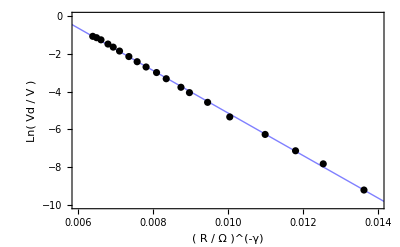

```mathematica
Show[plotfit2,plotdata2]
```

```mathematica
(*PARTE 5*)
```

```mathematica
(*hc/KTLambda mucho mayor a 1?*)
```

```mathematica
20697.704986641365*((25^0.8621819)/295)*((dataV/dataI)^(-0.8621819475302489))
```

{15.337,14.1144,13.2831,12.371,11.3088,10.6438,10.0985,9.84383,9.4015,9.11103,8.79681,8.52861,8.28012,8.00005,7.81052,7.65262,7.44344,7.31034,7.19611}

```mathematica
(*Rango de Ts*)
```

```mathematica
295*((dataV/dataI)/25)^0.8621819
```

{1349.53,1466.43,1558.2,1673.08,1830.23,1944.58,2049.57,2102.61,2201.53,2271.72,2352.86,2426.85,2499.69,2587.2,2649.98,2704.65,2780.66,2831.29,2876.23}

```mathematica
(*suponemos que L=15mm y diam=1, y que es un cilindro*)
```

```mathematica
Steo=N[2*Pi*(1/2)*15] (*en mm^2*)
```

47.1239

```mathematica
errSteo=2*Pi*0.5*1
```

3.14159